```mathematica
FusionAtlasPaths={"~/projects/fusionatlas/package/"};
$Path=$Path~Join~FusionAtlasPaths;
<<FusionAtlas`
```

```mathematica
g1=GraphFromString["bwd1v1v1v1p1v1x0p0x1duals1v1v1x2"];
g2=GraphFromString["bwd1v1v1v1p1v1x0p1x0duals1v1v1x2"];
```

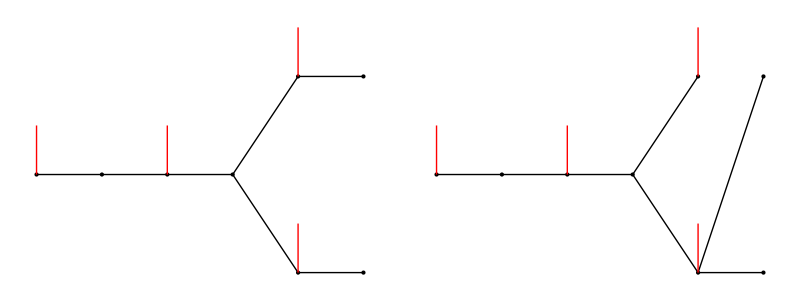

```mathematica
DisplayBigraph[{g1,g2}]
```

```mathematica
FindBigraphPairExtensionsUpToDepth[2.1][g1,g2,1]
```

FusionAtlas::loading: Loading precomputed data in FusionAtlas`Data`gbg1v1v1v1p1v1x0p0x1`PairExtensions`.

{{{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,0},{0,1}}],DualData[{1},{1},{1,2},{2,1}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}}],DualData[{1},{1},{1,2}]]}},{},{}}

```mathematica
{vines,weeds,{}}=FindBigraphPairExtensionsUpToDepth[2.2][g1,g2,1]
```

{{{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,0},{0,1}}],DualData[{1},{1},{1,2},{2,1}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}}],DualData[{1},{1},{1,2}]]}},{{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}},{{1,0}}],DualData[{1},{1},{1,2},{1}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,0},{1,0},{0,1}}],DualData[{1},{1},{1,2},{3,2,1}]]},{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}},{{1,0},{0,1}}],DualData[{1},{1},{1,2},{1,2}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,1}}],DualData[{1},{1},{1,2},{1}]]},{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}},{{1,0},{0,1}}],DualData[{1},{1},{1,2},{1,2}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,0},{1,0},{0,1},{0,1}}],DualData[{1},{1},{1,2},{4,2,3,1}]]}},{}}

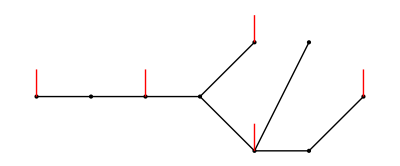
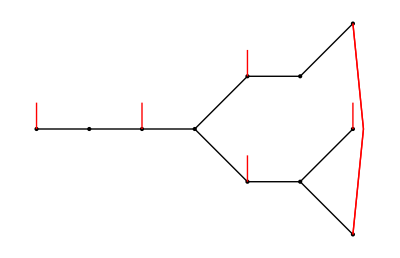
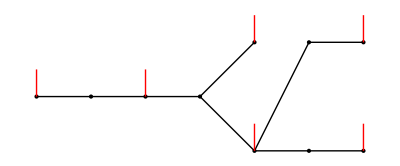
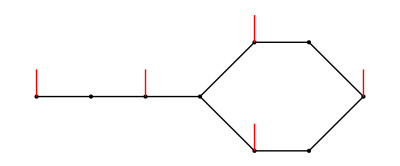
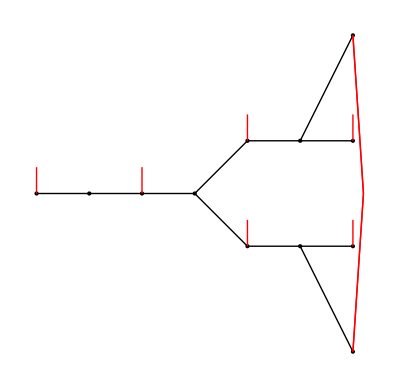
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[DisplayBigraph,weeds,{2}]
```

```mathematica
Map[GraphToString,weeds,{2}]
```

{{bwd1v1v1v1p1v1x0p1x0v1x0duals1v1v1x2v1,bwd1v1v1v1p1v1x0p0x1v1x0p1x0p0x1duals1v1v1x2v3x2x1},{bwd1v1v1v1p1v1x0p1x0v1x0p0x1duals1v1v1x2v1x2,bwd1v1v1v1p1v1x0p0x1v1x1duals1v1v1x2v1},{bwd1v1v1v1p1v1x0p1x0v1x0p0x1duals1v1v1x2v1x2,bwd1v1v1v1p1v1x0p0x1v1x0p1x0p0x1p0x1duals1v1v1x2v4x2x3x1}}

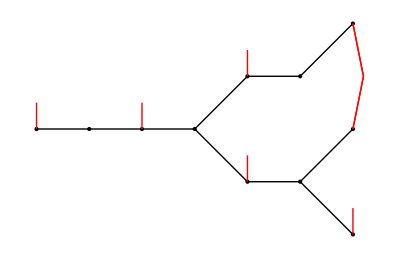
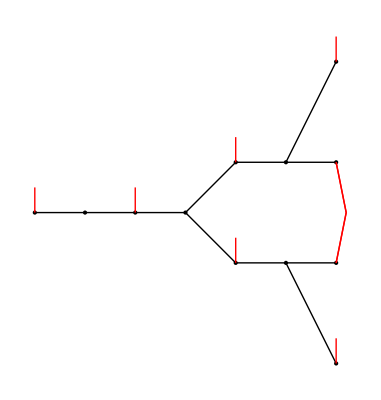
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[DisplayBigraph,{{"bwd1v1v1v1p1v1x0p0x1v1x1duals1v1v1x2v1","bwd1v1v1v1p1v1x0p1x0v1x0p0x1duals1v1v1x2v1x2"},{"bwd1v1v1v1p1v1x0p0x1v1x0p1x0p0x1duals1v1v1x2v1x3x2","bwd1v1v1v1p1v1x0p1x0v1x0duals1v1v1x2v1"},{"bwd1v1v1v1p1v1x0p0x1v1x0p1x0p0x1p0x1duals1v1v1x2v1x3x2x4","bwd1v1v1v1p1v1x0p1x0v1x0p0x1duals1v1v1x2v1x2"}},{2}]
```

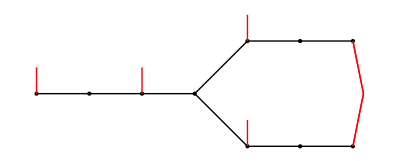
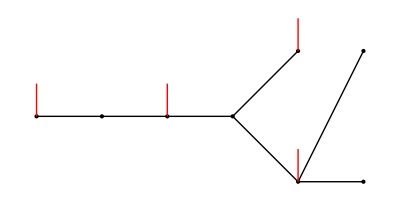

```mathematica
Map[DisplayBigraph,vines,{2}]
```

```mathematica
Map[GraphToString,vines,{2}]
```

{{bwd1v1v1v1p1v1x0p0x1v1x0p0x1duals1v1v1x2v2x1,bwd1v1v1v1p1v1x0p1x0duals1v1v1x2}}

```mathematica
{vines,weeds,{}}=FindBigraphPairExtensionsUpToDepth[2.17534][g1,g2,∞]
```

{{{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,0},{0,1}}],DualData[{1},{1},{1,2},{2,1}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}}],DualData[{1},{1},{1,2}]]},{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}},{{1,0},{0,1}}],DualData[{1},{1},{1,2},{1,2}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,1}}],DualData[{1},{1},{1,2},{1}]]},{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,0},{1,0},{0,1}},{{0,0,1}},{{1}}],DualData[{1},{1},{1,2},{3,2,1},{1}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}},{{1,0}},{{1}}],DualData[{1},{1},{1,2},{1}]]},{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,0},{1,0},{0,1}},{{0,1,0},{0,0,1}},{{1,0},{0,1},{0,1}}],DualData[{1},{1},{1,2},{3,2,1},{3,2,1}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}},{{1,0}},{{1},{1}}],DualData[{1},{1},{1,2},{1}]]},{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}},{{1,0}},{{1},{1}},{{1,0}}],DualData[{1},{1},{1,2},{1},{1}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,0},{1,0},{0,1}},{{0,1,0},{0,0,1}},{{1,1}}],DualData[{1},{1},{1,2},{3,2,1},{1}]]},{BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{0,1}},{{1,0},{1,0},{0,1}},{{0,1,0},{0,0,1}},{{1,0},{1,0},{0,1},{0,1}},{{0,0,0,1}},{{1}}],DualData[{1},{1},{1,2},{3,2,1},{4,2,3,1},{1}]],BigraphWithDuals[GradedBigraph[{{1}},{{1}},{{1}},{{1},{1}},{{1,0},{1,0}},{{1,0}},{{1},{1}},{{1,0}},{{1}}],DualData[{1},{1},{1,2},{1},{1}]]}},{},{}}

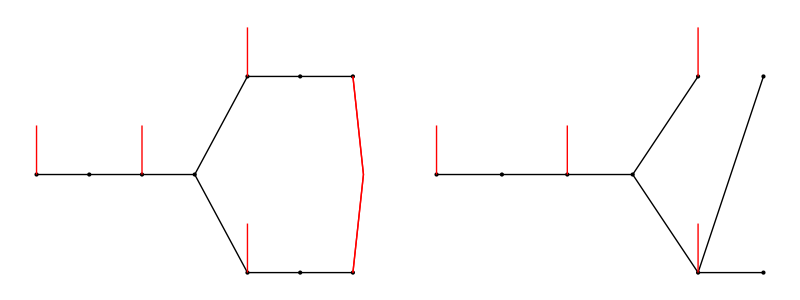
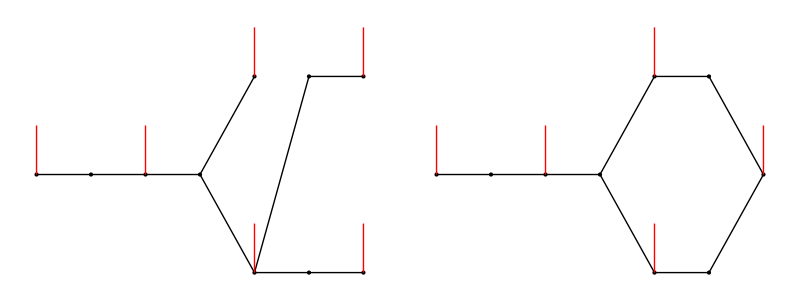
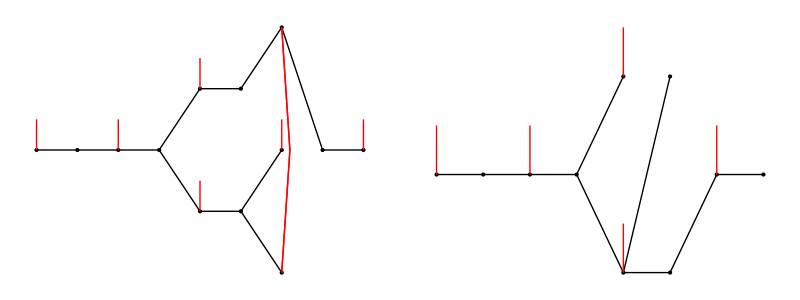
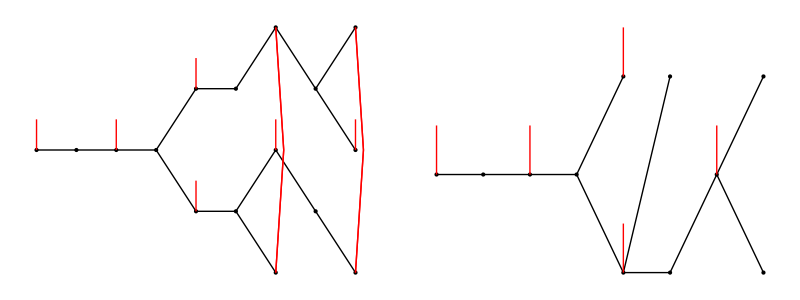
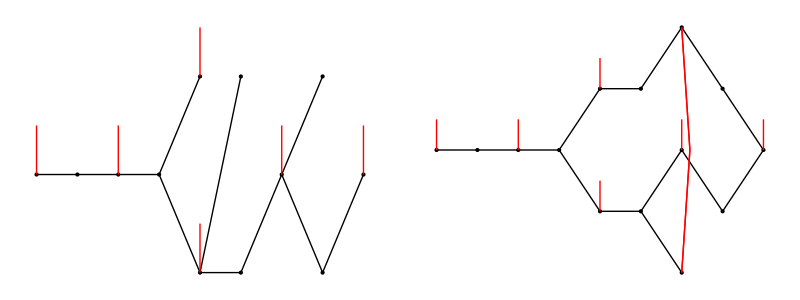
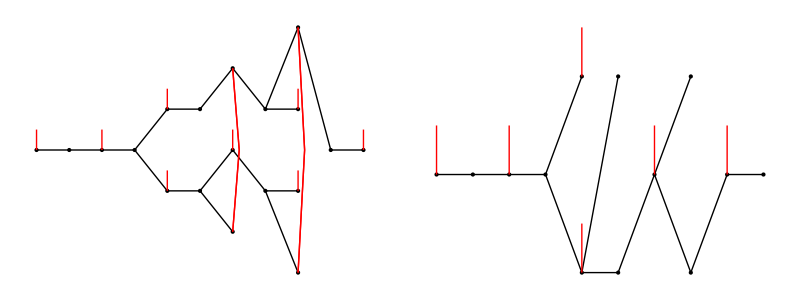

```mathematica
DisplayBigraph/@vines
```

```mathematica
Map[GraphToString,vines,{2}]
```

{{bwd1v1v1v1p1v1x0p0x1v1x0p0x1duals1v1v1x2v2x1,bwd1v1v1v1p1v1x0p1x0duals1v1v1x2},{bwd1v1v1v1p1v1x0p1x0v1x0p0x1duals1v1v1x2v1x2,bwd1v1v1v1p1v1x0p0x1v1x1duals1v1v1x2v1},{bwd1v1v1v1p1v1x0p0x1v1x0p1x0p0x1v0x0x1v1duals1v1v1x2v3x2x1v1,bwd1v1v1v1p1v1x0p1x0v1x0v1duals1v1v1x2v1},{bwd1v1v1v1p1v1x0p0x1v1x0p1x0p0x1v0x1x0p0x0x1v1x0p0x1p0x1duals1v1v1x2v3x2x1v3x2x1,bwd1v1v1v1p1v1x0p1x0v1x0v1p1duals1v1v1x2v1},{bwd1v1v1v1p1v1x0p1x0v1x0v1p1v1x0duals1v1v1x2v1v1,bwd1v1v1v1p1v1x0p0x1v1x0p1x0p0x1v0x1x0p0x0x1v1x1duals1v1v1x2v3x2x1v1},{bwd1v1v1v1p1v1x0p0x1v1x0p1x0p0x1v0x1x0p0x0x1v1x0p1x0p0x1p0x1v0x0x0x1v1duals1v1v1x2v3x2x1v4x2x3x1v1,bwd1v1v1v1p1v1x0p1x0v1x0v1p1v1x0v1duals1v1v1x2v1v1}}